## σ_T

```mathematica
σTsmall[β_]:=2 π β^2(1/2+β^2(-BesselK[1, β]^2+BesselK[0,β]BesselK[2,β]))
```

### Attractive

```mathematica
γ[β_]:=Sqrt[π/β] Erfi[Sqrt[ProductLog[2β]/2]]-1/ProductLog[2β]
```

```mathematica
σTlargeatt[β_]:=π((1+Log[β]-1/(2 Log[β]))^2-1/γ[β]^2)
```

```mathematica
βlow=1;
βhigh=50;
```

```mathematica
sol=FindRoot[{σTsmall[βlow]==a π*ProductLog[b*βlow]^2,σTlargeatt[βhigh]==a π*ProductLog[b*βhigh]^2},{{a,0.5},{b,3}}]
```

{a→1.17581,b→3.85656}

```mathematica
σT[β_]:=Piecewise[{{σTsmall[β],β≤βlow},{a π*ProductLog[b*β]^2/.sol,β>βlow&&β<βhigh},{σTlargeatt[β],β≥βhigh}}]
```

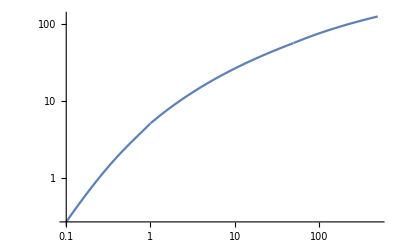

```mathematica
LogLogPlot[σT[β],{β,0.1*βlow,10*βhigh}]
```

### Repulsive

```mathematica
σTlargerep[β_]:=π*1.20*ProductLog[2β]^2
```

```mathematica
βlow=1;
βhigh=10;
```

```mathematica
sol=FindRoot[{σTsmall[βlow]==a π*ProductLog[b*βlow]^2,σTlargerep[βhigh]==a π*ProductLog[b*βhigh]^2},{{a,0.5},{b,3}}]
```

{a→0.461105,b→12.4722}

```mathematica
σT[β_]:=Piecewise[{{σTsmall[β],β≤βlow},{a π*ProductLog[b*β]^2/.sol,β>βlow&&β<βhigh},{σTlargerep[β],β≥βhigh}}]
```

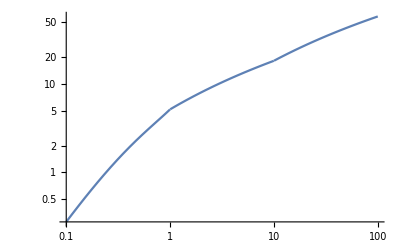

```mathematica
LogLogPlot[σT[β],{β,0.1*βlow,10*βhigh}]
```

## σ_V

```mathematica
σVsmall[β_]:=4 π β^2(1/2+4β^2(-BesselK[1,2 β]^2+BesselK[0,2β]BesselK[2,2β]))
```

### Attractive

```mathematica
σVlargeatt[β_]:=π/2(1+Log[β]-1/(2 Log[β]))^2
```

```mathematica
βlow=0.5;
βhigh=20;
```

```mathematica
sol=FindRoot[{σVsmall[βlow]==a π*ProductLog[b*βlow]^2,σVlargeatt[βhigh]==a π*ProductLog[b*βhigh]^2},{{a,0.5},{b,3}}]
```

{a→0.481683,b→9.64499}

```mathematica
σV[β_]:=Piecewise[{{σVsmall[β],β≤βlow},{a π*ProductLog[b*β]^2/.sol,β>βlow&&β<βhigh},{σVlargeatt[β],β≥βhigh}}]
```

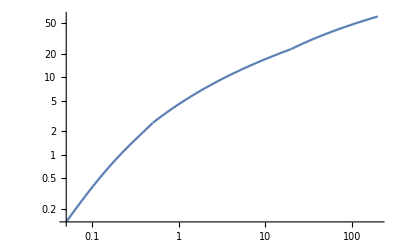

```mathematica
LogLogPlot[σV[β],{β,0.1*βlow,10*βhigh}]
```

### Repulsive

```mathematica
σVlargerep[β_]:=0.793 π ProductLog[2β]^2+π/2(ProductLog[4π β^2]^2/4-ProductLog[2β]^2)
```

```mathematica
βlow=0.5;
βhigh=5;
```

```mathematica
sol=FindRoot[{σVsmall[βlow]==a π*ProductLog[b*βlow]^2,σVlargerep[βhigh]==a π*ProductLog[b*βhigh]^2},{{a,0.5},{b,3}}]
```

{a→0.294701,b→17.7402}

```mathematica
σV[β_]:=Piecewise[{{σVsmall[β],β≤βlow},{a π*ProductLog[b*β]^2/.sol,β>βlow&&β<βhigh},{σVlargerep[β],β≥βhigh}}]
```

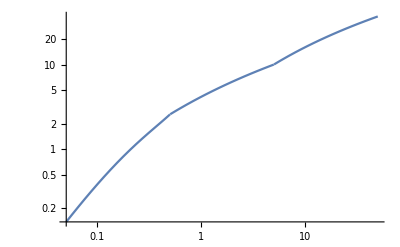

```mathematica
LogLogPlot[σV[β],{β,0.1*βlow,10*βhigh}]
```